```mathematica
ex=kontrol[[26]]
```

{6.6,3.,4.4,1.4,2}

```mathematica
classes={"Iris-setosa","Iris-versicolor","Iris-virginica"};
```

```mathematica
r[u_,x_,i_]:=Abs[u[[i]]-x[[i]]]
```

```mathematica
w[i_,u_]:=Boole[i==1]
```

```mathematica
w1=Boole[#1==1]&;
```

```mathematica
sortByFunc[data_,u_,func_]:=SortBy[data,func]
```

```mathematica
gamma[y_,u_,data_,w_]:=Module[{sorted},
sorted=SortBy[data,r[u,#,{4}]&];
Sum[w[i,u]Boole[y ==sorted[[i]][[5]] ],{i,1,Length[data]}]]
```

```mathematica
oneNN[u_,data_]:=ArgMax[{gamma[x,u,data,w1],x∈ImplicitRegion[1≤x≤3,x]&&x∈Integers},x,WorkingPrecision->20]
```

```mathematica
oneNN[ex,learn]
```

{2}

```mathematica
Table[Flatten[{oneNN[kontrol[[i]],learn],kontrol[[i]]},1],{i,1,Length[kontrol]}]//TableForm;
```

KNN 1 ficha

```mathematica
Clear[wk]
```

```mathematica
wk[k_]:=Boole[#1≤ k]&
```

```mathematica
kNN[u_,data_,k_]:=ArgMax[{gamma[x,u,data,wk[k]],x∈ImplicitRegion[1≤x≤3,x]&&x∈Integers},x,WorkingPrecision->20]
```

```mathematica
Table[Flatten[{kNN[kontrol[[i]],learn,3],kontrol[[i]]},1],{i,1,Length[kontrol]}]//TableForm;
```

KNN k fiches

```mathematica
r[u_,x_,i_]:=Module[{s},
s=0;
For[k=1,k<=Length[i],k++,s=s+Abs[u[[i[[k]]]]-x[[i[[k]]]]]^2];
√s]
```

```mathematica
gamma34[y_,u_,data_,w_]:=Module[{sorted},
sorted=sortByFunc[data,u,r[u,#,{1,2,3,4}]&];
Sum[w[i,u]Boole[y ==sorted[[i]][[5]] ],{i,1,Length[data]}]]
```

```mathematica
kkNN[u_,data_,k_]:=ArgMax[{gamma34[x,u,data,wk[k]],x∈ImplicitRegion[1≤x≤3,x]&&x∈Integers},x,WorkingPrecision->20][[1]]
```

```mathematica
ex
```

{6.6,3.,4.4,1.4,2}

```mathematica
Table[Flatten[{kkNN[kontrol[[i]],learn,6],kontrol[[i]]},1],{i,1,Length[kontrol]}]//TableForm;
```

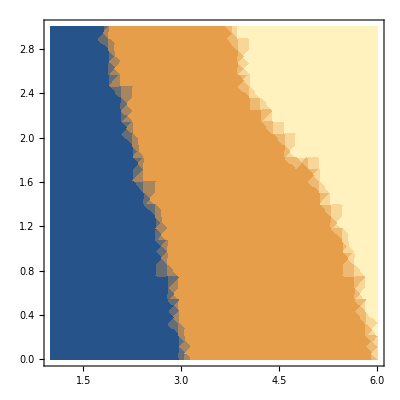

```mathematica
DensityPlot[kkNN[{6,3,z,y,2},learn,6],{z,1,6},{y,0,3}]
```

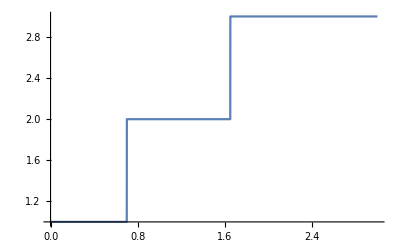

```mathematica
Plot[kNN[{6,3,1,y,2},learn,6],{y,0,3}]
```

```mathematica
p2=ListPlot[Partition[Table[{#[[i,3]],#[[i,4]]},{i,1,75}],25],ImageSize->300,PlotStyle->{Red,Green,Blue}]&[kontrol];
```

```mathematica
p3=ListPlot[Partition[Table[{#[[i,3]],#[[i,4]]},{i,1,75}],25],ImageSize->300,PlotStyle->{Pink,Black,Red}]&[learn];
```

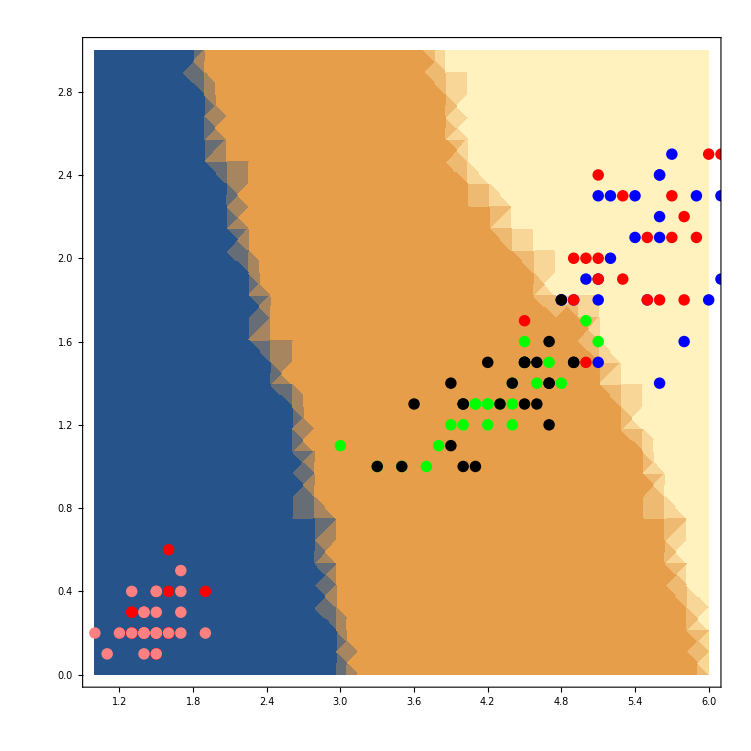

```mathematica
Show[{DensityPlot[kkNN[{6,3,z,y,2},learn,6],{z,1,6},{y,0,3}],p2,p3}]
```

```mathematica
kkNN[{6,3,2.2,2.5,2},learn,6]
```

2

```mathematica
looSum[k_,data_]:=Sum[Boole[kkNN[data[[i]],Delete[data,i],k]≠data[[i]][[5]]],{i,1,Length[data]}]
```

```mathematica
Table[looSum[i,learn],{i,1,19}]
```

{4,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3}

```mathematica
LOO[data_]:=ArgMin[looSum[x,data],x,Integers,WorkingPrecision->20]
```

```mathematica
LOO[learn]
```

84

```mathematica
NMaximize[Sum[Boole[kkNN[kontrol[[i]],learn,x]==kontrol[[i]][[5]]],{i,1,Length[learn]}],x,Integers,WorkingPrecision->2]
```

{71.,{x→761}}

```mathematica
Sum[Boole[kkNN[kontrol[[i]],learn,1]==kontrol[[i]][[5]]],{i,1,Length[learn]}]
```

70

```mathematica
Sum[Boole[kkNN[kontrol[[i]],learn,4]!=kontrol[[i]][[5]]],{i,1,Length[learn]}]
```

4

```mathematica
Table[Flatten[{kkNN[kontrol[[i]],learn,4],kontrol[[i]]},1],{i,1,Length[kontrol]}]//TableForm
```

1 | 5. | 3. | 1.6 | 0.2 | 1
1 | 5. | 3.4 | 1.6 | 0.4 | 1
1 | 5.2 | 3.5 | 1.5 | 0.2 | 1
1 | 5.2 | 3.4 | 1.4 | 0.2 | 1
1 | 4.7 | 3.2 | 1.6 | 0.2 | 1
1 | 4.8 | 3.1 | 1.6 | 0.2 | 1
1 | 5.4 | 3.4 | 1.5 | 0.4 | 1
1 | 5.2 | 4.1 | 1.5 | 0.1 | 1
1 | 5.5 | 4.2 | 1.4 | 0.2 | 1
1 | 4.9 | 3.1 | 1.5 | 0.1 | 1
1 | 5. | 3.2 | 1.2 | 0.2 | 1
1 | 5.5 | 3.5 | 1.3 | 0.2 | 1
1 | 4.9 | 3.1 | 1.5 | 0.1 | 1
1 | 4.4 | 3. | 1.3 | 0.2 | 1
1 | 5.1 | 3.4 | 1.5 | 0.2 | 1
1 | 5. | 3.5 | 1.3 | 0.3 | 1
1 | 4.5 | 2.3 | 1.3 | 0.3 | 1
1 | 4.4 | 3.2 | 1.3 | 0.2 | 1
1 | 5. | 3.5 | 1.6 | 0.6 | 1
1 | 5.1 | 3.8 | 1.9 | 0.4 | 1
1 | 4.8 | 3. | 1.4 | 0.3 | 1
1 | 5.1 | 3.8 | 1.6 | 0.2 | 1
1 | 4.6 | 3.2 | 1.4 | 0.2 | 1
1 | 5.3 | 3.7 | 1.5 | 0.2 | 1
1 | 5. | 3.3 | 1.4 | 0.2 | 1
2 | 6.6 | 3. | 4.4 | 1.4 | 2
2 | 6.8 | 2.8 | 4.8 | 1.4 | 2
2 | 6.7 | 3. | 5. | 1.7 | 2
2 | 6. | 2.9 | 4.5 | 1.5 | 2
2 | 5.7 | 2.6 | 3.5 | 1. | 2
2 | 5.5 | 2.4 | 3.8 | 1.1 | 2
2 | 5.5 | 2.4 | 3.7 | 1. | 2
2 | 5.8 | 2.7 | 3.9 | 1.2 | 2
2 | 6. | 2.7 | 5.1 | 1.6 | 2
2 | 5.4 | 3. | 4.5 | 1.5 | 2
2 | 6. | 3.4 | 4.5 | 1.6 | 2
2 | 6.7 | 3.1 | 4.7 | 1.5 | 2
2 | 6.3 | 2.3 | 4.4 | 1.3 | 2
2 | 5.6 | 3. | 4.1 | 1.3 | 2
2 | 5.5 | 2.5 | 4. | 1.3 | 2
2 | 5.5 | 2.6 | 4.4 | 1.2 | 2
2 | 6.1 | 3. | 4.6 | 1.4 | 2
2 | 5.8 | 2.6 | 4. | 1.2 | 2
2 | 5. | 2.3 | 3.3 | 1. | 2
2 | 5.6 | 2.7 | 4.2 | 1.3 | 2
2 | 5.7 | 3. | 4.2 | 1.2 | 2
2 | 5.7 | 2.9 | 4.2 | 1.3 | 2
2 | 6.2 | 2.9 | 4.3 | 1.3 | 2
2 | 5.1 | 2.5 | 3. | 1.1 | 2
2 | 5.7 | 2.8 | 4.1 | 1.3 | 2
3 | 7.2 | 3.2 | 6. | 1.8 | 3
2 | 6.2 | 2.8 | 4.8 | 1.8 | 3
2 | 6.1 | 3. | 4.9 | 1.8 | 3
3 | 6.4 | 2.8 | 5.6 | 2.1 | 3
3 | 7.2 | 3. | 5.8 | 1.6 | 3
3 | 7.4 | 2.8 | 6.1 | 1.9 | 3
3 | 7.9 | 3.8 | 6.4 | 2. | 3
3 | 6.4 | 2.8 | 5.6 | 2.2 | 3
2 | 6.3 | 2.8 | 5.1 | 1.5 | 3
3 | 6.1 | 2.6 | 5.6 | 1.4 | 3
3 | 7.7 | 3. | 6.1 | 2.3 | 3
3 | 6.3 | 3.4 | 5.6 | 2.4 | 3
3 | 6.4 | 3.1 | 5.5 | 1.8 | 3
2 | 6. | 3. | 4.8 | 1.8 | 3
3 | 6.9 | 3.1 | 5.4 | 2.1 | 3
3 | 6.7 | 3.1 | 5.6 | 2.4 | 3
3 | 6.9 | 3.1 | 5.1 | 2.3 | 3
3 | 5.8 | 2.7 | 5.1 | 1.9 | 3
3 | 6.8 | 3.2 | 5.9 | 2.3 | 3
3 | 6.7 | 3.3 | 5.7 | 2.5 | 3
3 | 6.7 | 3. | 5.2 | 2.3 | 3
3 | 6.3 | 2.5 | 5. | 1.9 | 3
3 | 6.5 | 3. | 5.2 | 2. | 3
3 | 6.2 | 3.4 | 5.4 | 2.3 | 3
3 | 5.9 | 3. | 5.1 | 1.8 | 3

```mathematica
f[func_,w_]:=Plot[{func,Sin[x],Cos[x]},{x,1,10},PlotLabels->w]
```

```mathematica
Clear["Global`*"]
```

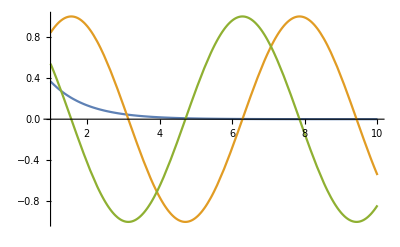

```mathematica
f[Exp[-x],{}]
```